50

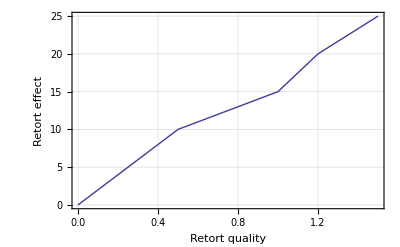

-Graphics-

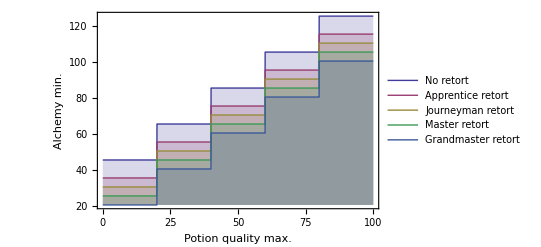

-Graphics-

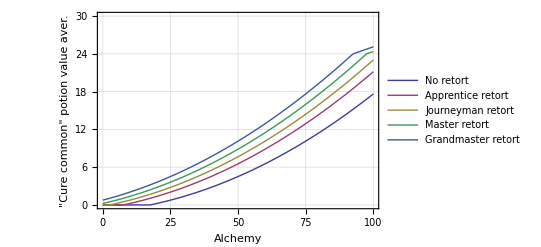

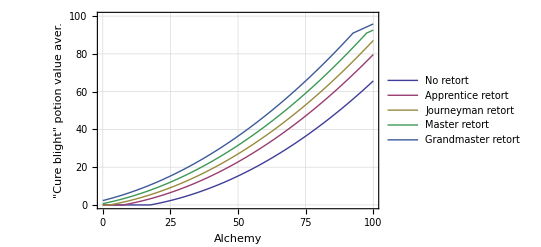

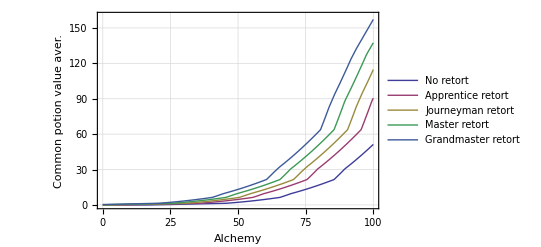

```mathematica
luck=50
RetortValue[rq_]:= If[rq < 0.5,-20+20rq,If[rq<1,-10+10(rq-0.5),If[rq<1.2,-5+25(rq-1),(50/3)(rq-1.2)]]]
LuckValue[kv_]:=If[kv<40,kv-40,If[kv<60,(1/4)(kv-40),5+(1/8)(kv-60)]]
PsuccBase[av_,rq_]:=av+RetortValue[rq]+LuckValue[luck]
Psucc[av_,rq_]:=If[PsuccBase[av,rq]<0,0,If[PsuccBase[av,rq]>100,100, PsuccBase[av,rq]]]
PotionMinBase[av_,rq_]:=PsuccBase[av,rq]-32
PotionMaxBase[av_,rq_]:=PotionMinBase[av,rq]+24
PotionValue[b_]:=If[b<20,20,If[b<40,40,If[b<60,60,If[b<80,80,100]]]]
PotionCost[b_]:=If[b<20,5,If[b<40,15,If[b<60,35,If[b<80,80,175]]]]
PotionMinQ[av_,rq_]:=PotionValue[PotionMinBase[av,rq]]
PotionMaxQ[av_,rq_]:=PotionValue[PotionMaxBase[av,rq]]
PotionInterQ[av_,rq_]:=PotionMaxQ[av,rq] - 20
PotionMinQP[av_,rq_]:=(PotionMinQ[av,rq]-PotionMinBase[av,rq])/24
PotionInterQP[av_,rq_]:=(PotionInterQ[av,rq]-PotionMinQ[av,rq])/24
PotionMaxQP[av_,rq_]:=(PotionMaxBase[av,rq]-PotionInterQ[av,rq])/24
Potion5V[av_,rq_]:=(Psucc[av,rq]/100)(PotionMinQP[av,rq]PotionCost[PotionMinBase[av,rq]]+PotionMaxQP[av,rq]PotionCost[PotionMaxBase[av,rq]]+PotionInterQP[av,rq]PotionCost[PotionInterQ[av,rq]-1])
PotionMax[av_,rq_]:=If[PsuccBase[av,rq]≤0,0, PotionValue[PotionMaxBase[av,rq]]]
PotionAlchemyBase[rq_,p_]:=First[av/.Solve[PotionMaxBase[av,rq]==p,av]]
PotionAlchemy[rq_,p_]:=PotionAlchemyBase[rq,PotionValue[p]]
Potion2Q[av_,rq_, pin_]:=(Psucc[av,rq]/100)(If[PsuccBase[av,rq]>pin,1/2,0]+(PsuccBase[av,rq]-pin +If[PsuccBase[av,rq]>pin,0,100])(1/200))

getTheGraphics[g_Graphics]:=g;
getTheGraphics[plot_Legended]:=Module[{gr},ToBoxes[plot/.Placed[i_,coords:_Symbol,f_]:>Placed[i,coords/.{Left->{-0.1,0.5},Right|After->{1.1,0.5},Top->{0.5,1.1},Bottom->{0.5,-0.1}},f]]/.g_GraphicsBox:>(gr=g;Break[Null,ReplaceAll]);
ToExpression[gr]]

Plot[20+RetortValue[rq],{rq,0,1.5},Frame->True,FrameLabel->{"Retort quality","Retort effect"},GridLines->Automatic,PlotRangePadding->None]
Plot[{Psucc[av,0],Psucc[av,0.5],Psucc[av,1],Psucc[av,1.2],Psucc[av,1.5]},{av,0,100},PlotRange->{0,100},Frame->True,GridLines->Automatic,PlotStyle->Thick,PlotRangePadding->None,PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort","Grandmaster retort"},FrameLabel->{"Alchemy","Success"},ImageSize->Large]//getTheGraphics
Plot[{PotionAlchemy[0,p],PotionAlchemy[0.5,p],PotionAlchemy[1,p],PotionAlchemy[1.2,p],PotionAlchemy[1.5,p]},{p,0,100},Frame->True,Filling->Bottom,PlotRangePadding->None,FrameLabel->{"Potion quality max.","Alchemy min."},PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort",
"Grandmaster retort"}]
Plot[{Potion2Q[av,0],Potion2Q[av,0.5],Potion2Q[av,1],Potion2Q[av,1.2],Potion2Q[av,1.5]},{av,0,100},PlotRange->{0,1},Frame->True,GridLines->Automatic,PlotStyle->Thick,PlotRangePadding->None,PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort","Grandmaster retort"},FrameLabel->{"Alchemy","\"Cure common\" potion output aver."}]
Plot[{30Potion2Q[av,0,40],30Potion2Q[av,0.5,40],30Potion2Q[av,1,40],30Potion2Q[av,1.2,40],30Potion2Q[av,1.5,40]},{av,0,100},PlotRange->{0,30},Frame->True,GridLines->Automatic,PlotStyle->Thick,PlotRangePadding->None,PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort","Grandmaster retort"},FrameLabel->{"Alchemy","\"Cure common\" potion value aver."}]
Plot[{130Potion2Q[av,0,60],130Potion2Q[av,0.5,60],130Potion2Q[av,1,60],130Potion2Q[av,1.2,60],130Potion2Q[av,1.5,60]},{av,0,100},PlotRange->{0,100},Frame->True,GridLines->Automatic,PlotStyle->Thick,PlotRangePadding->None,PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort","Grandmaster retort"},FrameLabel->{"Alchemy","\"Cure blight\" potion value aver."}]
Plot[{Potion5V[av,0],Potion5V[av,0.5],Potion5V[av,1],Potion5V[av,1.2],Potion5V[av,1.5]},{av,0,100},Frame->True,GridLines->Automatic,PlotStyle->Thick,PlotRangePadding->None,PlotLegends->{"No retort","Apprentice retort","Journeyman retort","Master retort","Grandmaster retort"},FrameLabel->{"Alchemy","Common potion value aver."},PlotRange->{0,160}]
```